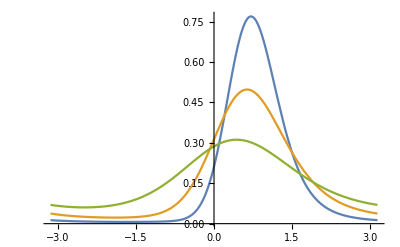

```mathematica
psln[κk_,ϵk_]:=NDSolveValue[{D[(-1+κ Sin[Δ])p[Δ],Δ]+ϵ^2 D[p[Δ],Δ,Δ]==0,p[-π]==p[π],p[0]==1}/.{κ->κk,ϵ->ϵk},p,Δ];
f1=psln[1.5,0.5];
f2=psln[1.5,0.75];
f3=psln[1.5,1.25];
n1=NIntegrate[f1[Δ],{Δ,-π,π}];
n2=NIntegrate[f2[Δ],{Δ,-π,π}];
n3=NIntegrate[f3[Δ],{Δ,-π,π}];
Plot[{f1[Δ]/n1,f2[Δ]/n2,f3[Δ]/n3},{Δ,-π,π},PlotRange->All]
```

```mathematica
psln[0.1,0.5]
```

InterpolatingFunction[…]

```mathematica
(* Fourier approach? *)
D[(-1+κ Sin[Δ])p[Δ],Δ]+ϵ^2 D[p[Δ],Δ,Δ]==0
```

κ Cos[Δ] p[Δ]+(-1+κ Sin[Δ]) p'[Δ]+ϵ^2 p''[Δ]==0

```mathematica
pFourier=Sum[a[n]Exp[I n Δ],{n,0,2}]+Sum[Conjugate[a[-n]]Exp[I n Δ],{n,-2,-1}]
```

a[0]+ⅇ^(ⅈ Δ) a[1]+ⅇ^(2 ⅈ Δ) a[2]+ⅇ^(-ⅈ Δ) Conjugate[a[1]]+ⅇ^(-2 ⅈ Δ) Conjugate[a[2]]

```mathematica
expr=κ Cos[Δ] (pFourier)+(-1+κ Sin[Δ]) (D[pFourier,Δ])+ϵ^2 (D[pFourier,Δ,Δ])//TrigExpand
```

1/2 ⅇ^(-ⅈ Δ) κ a[0]+1/2 ⅇ^(ⅈ Δ) κ a[0]-ⅈ ⅇ^(ⅈ Δ) a[1]-ⅇ^(ⅈ Δ) ϵ^2 a[1]+ⅇ^(2 ⅈ Δ) κ a[1]-2 ⅈ ⅇ^(2 ⅈ Δ) a[2]-4 ⅇ^(2 ⅈ Δ) ϵ^2 a[2]-1/2 ⅇ^(ⅈ Δ) κ a[2]+3/2 ⅇ^(3 ⅈ Δ) κ a[2]+ⅈ ⅇ^(-ⅈ Δ) Conjugate[a[1]]-ⅇ^(-ⅈ Δ) ϵ^2 Conjugate[a[1]]+ⅇ^(-2 ⅈ Δ) κ Conjugate[a[1]]+2 ⅈ ⅇ^(-2 ⅈ Δ) Conjugate[a[2]]-4 ⅇ^(-2 ⅈ Δ) ϵ^2 Conjugate[a[2]]-1/2 ⅇ^(-ⅈ Δ) κ Conjugate[a[2]]+3/2 ⅇ^(-3 ⅈ Δ) κ Conjugate[a[2]]

```mathematica
Collect[expr,E^_]
```

3/2 ⅇ^(3 ⅈ Δ) κ a[2]+ⅇ^(2 ⅈ Δ) (κ a[1]-2 ⅈ a[2]-4 ϵ^2 a[2])+ⅇ^(ⅈ Δ) (1/2 κ a[0]-ⅈ a[1]-ϵ^2 a[1]-1/2 κ a[2])+3/2 ⅇ^(-3 ⅈ Δ) κ Conjugate[a[2]]+ⅇ^(-2 ⅈ Δ) (κ Conjugate[a[1]]+2 ⅈ Conjugate[a[2]]-4 ϵ^2 Conjugate[a[2]])+ⅇ^(-ⅈ Δ) (1/2 κ a[0]+ⅈ Conjugate[a[1]]-ϵ^2 Conjugate[a[1]]-1/2 κ Conjugate[a[2]])

```mathematica
eq1=κ a[1]-2 ⅈ a[2]-4 ϵ^2 a[2]==0;
eq2=1/2 κ a[0]-ⅈ a[1]-ϵ^2 a[1]-1/2 κ a[2]==0;
slnFourier=Solve[{eq1,eq2},{a[1],a[2]}]//Simplify
```

{{a[1]→(2 (ⅈ+2 ϵ^2) κ a[0])/(-4+12 ⅈ ϵ^2+8 ϵ^4+κ^2),a[2]→(κ^2 a[0])/(-4+12 ⅈ ϵ^2+8 ϵ^4+κ^2)}}

```mathematica
Assuming[{ϵ>0,κ>0},pFourier/.slnFourier//Simplify]//ComplexExpand//Simplify
```

{(a[0] (16+80 ϵ^4+64 ϵ^8-8 κ^2+16 ϵ^4 κ^2+κ^4+8 ϵ^2 κ (2+8 ϵ^4+κ^2) Cos[Δ]+2 κ^2 (-4+8 ϵ^4+κ^2) Cos[2 Δ]+16 κ Sin[Δ]+64 ϵ^4 κ Sin[Δ]-4 κ^3 Sin[Δ]+24 ϵ^2 κ^2 Sin[2 Δ]))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))}

```mathematica
(* The integral over all non-constant Fourier terms is zero, so to normalize, a[0]=1/(2π), obviously... *)
```

```mathematica
(* Normalize! *)
pFourierExp[Δ_,ϵ_,κ_]:=((16+80 ϵ^4+64 ϵ^8-8 κ^2+16 ϵ^4 κ^2+κ^4+8 ϵ^2 κ (2+8 ϵ^4+κ^2) Cos[Δ]+2 κ^2 (-4+8 ϵ^4+κ^2) Cos[2 Δ]+16 κ Sin[Δ]+64 ϵ^4 κ Sin[Δ]-4 κ^3 Sin[Δ]+24 ϵ^2 κ^2 Sin[2 Δ]))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))/(2π)
```

```mathematica
(* Check numerics *)
NIntegrate[f1[Δ]Cos[Δ]/n1,{Δ,-π,π}]
Integrate[pFourierExp[Δ,0.5,0.05]Cos[Δ],{Δ,-π,π}]
```

0.00589371

0.00589309

```mathematica
(* Expression for <Cos[Δ]> *)
Integrate[pFourierExp[Δ,ϵ,κ]Cos[Δ],{Δ,-π,π}]//Simplify
```

(4 ϵ^2 κ (2+8 ϵ^4+κ^2))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))

```mathematica
RsqApprox[ϵ_,κ_]:=Piecewise[{{1/2+1/2((4 ϵ^2 κ (2+8 ϵ^4+κ^2))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))),κ<1},{1/2+1/2Sqrt[κ^2-1]/κ -ϵ^2/(8κ),κ≥1}}]
Rsqr[κ_]:=Piecewise[{{1/2,κ≤1},{(κ+√(κ^2-1))/(2 κ),κ>1}}]
```

```mathematica
Plot[{Rsqr[κ],RsqApprox[0.25,κ],RsqApprox[0.5,κ]},{κ,0,2},AxesLabel->{κ,⟨R^2⟩},PlotLabels->{"ϵ=0","ϵ=0.25","ϵ=0.5"}]
```

-Graphics-

```mathematica
(* Find optimum  *)
```

```mathematica
D[1/2+1/2((4 ϵ^2 κ (2+8 ϵ^4+κ^2))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))),ϵ]//Simplify
```

-(4 ϵ κ (-32+512 ϵ^12+6 κ^4-κ^6+64 ϵ^8 (-4+κ^2)-8 ϵ^4 (28-38 κ^2+κ^4)))/((64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))^2)

```mathematica
slnepsmax=Solve[-(4 ϵ κ (-32+512 ϵ^12+6 κ^4-κ^6+64 ϵ^8 (-4+κ^2)-8 ϵ^4 (28-38 κ^2+κ^4)))/((64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))^2)==0,ϵ];
```

```mathematica
Series[ϵ/.slnepsmax[[5]],{κ,0,6}]//Normal
```

1-(23 κ^2)/200-(16701 κ^4)/400000-(9121703 κ^6)/400000000

```mathematica
epsMax[κ_]:=1-(23 κ^2)/200-(16701 κ^4)/400000-(9121703 κ^6)/400000000
```

```mathematica
Plot[{RsqApprox[ϵ,0.95],RsqApprox[ϵ,0.5],RsqApprox[ϵ,0.2]},{ϵ,0,2},AxesLabel->{ϵ,⟨R^2⟩},PlotLabels->{"κ=0.95","κ=0.5","κ=0.2"}];
Show[p,ListPlot[{{epsMax[0.95],RsqApprox[epsMax[0.95],0.95]},{epsMax[0.5],RsqApprox[epsMax[0.5],0.5]},{epsMax[0.2],RsqApprox[epsMax[0.2],0.2]}},PlotStyle->{Red}]]
```

-Graphics-

```mathematica
RsqrNum[κ_,ϵ_]:=Module[{pf},pf=NDSolveValue[{D[(1+κ Sin[Δ])p[Δ],Δ]+ϵ^2 D[p[Δ],Δ,Δ]==0,p[-π]==p[π],p[0]==1},p,Δ];NIntegrate[pf[Δ](1/2+1/2Cos[Δ]),{Δ,-π,π}]/NIntegrate[pf[Δ],{Δ,-π,π}]]
```

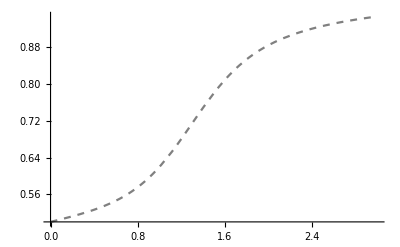

```mathematica
q=Plot[RsqrNum[κ,0.5],{κ,0,3},PlotPoints->5,PlotStyle->{{Dashed,Gray}}]
```

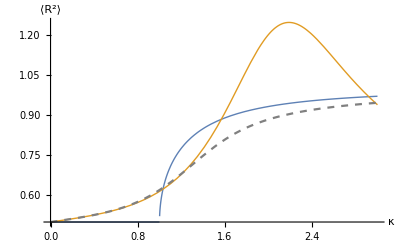

```mathematica
RsqrExtended[ϵ_,κ_]:=1/2+1/2((4 ϵ^2 κ (2+8 ϵ^4+κ^2))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2)))
Show[Plot[{Rsqr[κ],RsqrExtended[0.5,κ]},{κ,0,3},AxesLabel->{κ,⟨R^2⟩},PlotStyle->Thick],q]
```

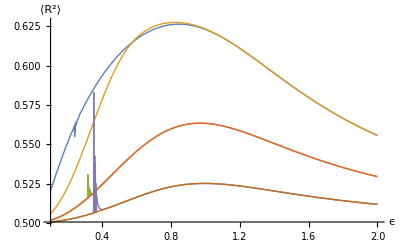

```mathematica
Show[Plot[{RsqrNum[0.95,ϵ],RsqApprox[ϵ,0.95],RsqrNum[0.5,ϵ],RsqApprox[ϵ,0.5],RsqrNum[0.2,ϵ],RsqApprox[ϵ,0.2]},{ϵ,0.1,2},AxesLabel->{ϵ,⟨R^2⟩},PlotStyle->Thick]]
```

```mathematica
(a+I b) Exp[I d]+(a-I b)Exp[-I d]//ComplexExpand
```

2 a Cos[d]-2 b Sin[d]

```mathematica
1/2(4 ϵ^2 κ (2+8 ϵ^4+κ^2))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))+1/2
```

1/2+(2 ϵ^2 κ (2+8 ϵ^4+κ^2))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2))

```mathematica
(1-(23 κ^2)/200-(16701 κ^4)/400000-(9121703 κ^6)/400000000)^2//Expand
```

1-(23 κ^2)/100-(1757 κ^4)/25000-(112517 κ^6)/3125000+(1118120077 κ^8)/160000000000+(152341561803 κ^10)/80000000000000+(83205465620209 κ^12)/160000000000000000

```mathematica
s=(1/2+(2 ϵ^2 κ (2+8 ϵ^4+κ^2))/(64 ϵ^8+(-4+κ^2)^2+16 ϵ^4 (5+κ^2)))/.ϵ->1-(23 κ^2)/200
```

1/2+(2 κ (1-(23 κ^2)/200)^2 (2+κ^2+8 (1-(23 κ^2)/200)^4))/(64 (1-(23 κ^2)/200)^8+(-4+κ^2)^2+16 (1-(23 κ^2)/200)^4 (5+κ^2))

```mathematica
Series[s,{κ,0,5}]
```

1/2+κ/8+κ^3/160+(177 κ^5)/80000+O[κ]^6